# Chapter. Variational Methods — The Action Principle

##### Paul Abbott paul.c.abbott@uwa.edu.au

## Introduction

Read Feynman's lecture on the action principle in

R P Feynman, R B Leighton, and M Sands, The Feynman Lectures on Physics, Addison-Wesley, 1963-65.

The papers by Edwin Taylor are both interesting and readable. For example, see

J Ogborn and E F Taylor, Quantum physics explains Newton's laws of motion, Physics Education, Vol. 40, No. 1, 2005, pages 26-34. ⊳ http://www.eftaylor.com/leastaction.html

Also, see

T A Moore, Least-Action Principle in Macmillan Encyclopedia of Physics, John Rigden, editor, Simon & Schuster Macmillan, 1996, Volume 2, page 840.

J Mathews and R L Walker, Mathematical Methods of Physics, W. A. Benjamin, New York, 1970.

The chapter on the calculus of variations is at a more advanced level, but is still readable.

## Lagrangian Dynamics and the Action Integral

### Lagrangian

The Lagrangian L==T-V is the difference between the kinetic energy T and the potential energy V. In general L depends upon position, velocity, and time.

#### Example: Lagrangian for a mass-spring system

The Lagrangian L for a mass attached to a spring is given by

L==1/2 m (ẋ)^2-1/2 k x^2.

### Action

What is the action? It is just L integrated over time:

S= ∫_t_1^t_2 Lⅆt.

#### Example: action for a mass-spring system

The action for a mass attached to a spring is given by

S= ∫_t_1^t_2 (1/2 m (ẋ)^2-1/2 k x^2)ⅆt.

### Principle of Least Action

Pierre Louis Moreau de Maupertuis (1698-1759) introduced the principle of least action around 1750, though his definition of action was imprecise. Maupertuis hoped that the principle might unify the laws of physics and support his proof of the existence of God.

Hamilton's variational principle—or the action principle—is an assertion about the nature of motion, from which the trajectory of an object subject to forces can be determined. The path of an object is the one that yields a stationary value for the action

δ S==δ ∫_t_1^t_2 Lⅆt==0,

where δ S denotes the variation in S.

Instead of thinking about an object accelerating in response to applied forces, you can think of them picking out the path with a stationary action.

From Moore (1996):

The least-action principle is an assertion about the nature of motion that provides an alternative approach to mechanics completely independent of Newton's laws. Not only does the least-action principle offer a means of formulating classical mechanics that is more flexible and powerful than Newtonian mechanics, [but also] variations on the least-action principle have proved useful in general relativity theory, quantum field theory, and particle physics. As a result, this principle lies at the core of much of contemporary theoretical physics.

The principle of least action has wide applicability in physics, from mechanics, through electricity and magnetism, quantum mechanics, special and general relativity—and it provides a deep foundation for advanced subjects and current research.

### Basics of calculus of variations

In these notes a functional—a function of a function—takes a function as input and returns a scalar.

Consider

ℱ(y, y',x),

which depends upon y, its derivative y', and x. The integral

ℐ[y]==∫_a^b ℱ(y(x), y'(x),x)ⅆx

is a functional. How can we choose the function y so that ℐ[y] is stationary?

Consider the replacement

y→y+α η

where α is small and η is arbitrary, except that η(a)==η(b)==0 (that is, the variation vanishes at the end points a and b).

#### Example: a simple variation

Here are two (smooth) curves joining the points P and Q, y and y+α η. In this example the variation η is controlled by the parameters c, d, and e:

```mathematica
Manipulate[Plot[{𝓎[x],𝓎[x]+α InterpolatingPolynomial[{{a,0},{b,0},{a+(b-a)/4,c},{a+(b-a)/2,d},{a+(3(b-a))/4,e}},x]},{x,a,b},AxesOrigin->{0,0},Ticks->{{{a,"a"},{b,"b"}},{{𝓎[a],HoldForm[y["a"]]},{𝓎[b],HoldForm[y["b"]]}}},Epilog->{Text["P",{a,𝓎[a]-0.5}],Text["Q",{b,𝓎[b]-0.5}],Red,Point[{a,𝓎[a]}],Point[{b,𝓎[b]}]},PlotRange->{{0,10},{0,10}},AxesLabel->{x,y}],{{a,2},1,4},{{b,7},5,8},{{α,0.3},0,1},{{c,1},-2,2},{{d,-1},-2,2},{{e,-1},-2,2},Initialization:>(𝓎[x_]:=-1/3 (x-4)^2+8)]
```

#### Stationarity

If ℐ[y] is to be stationary then

(ⅆℐ[y+α η]/ⅆα|)_(α==0)==0

for all η.

Compute the Taylor series expansion of ℱ with respect to α:

```mathematica
ℱ(y+α η, y'+α η',x)+O[α]^2
```

ℱ(y,y',x)+α (η' ℱ^(0,1,0)(y,y',x)+η ℱ^(1,0,0)(y,y',x))+O(α^2)

Hence

ℐ[y+α η]==∫_a^b ℱ(y+α η, y'+α η',x)ⅆx==ℐ[y]+α ∫_a^b ((∂ℱ)/(∂y)η+(∂ℱ)/(∂y')η')ⅆx+O(α^2),

so stationarity requires that

∫_a^b ((∂ℱ)/(∂y)η+(∂ℱ)/(∂y')η')ⅆx==0.

#### Euler-Lagrange equation

Integrating (∂ℱ)/(∂y')η' by parts,

(∫_a^b (∂ℱ)/(∂y')η' ⅆx==η (∂ℱ)/(∂y')|)_a^b-∫_a^b ⅆ_x((∂ℱ)/(∂y'))ηⅆx==-∫_a^b ⅆ_x((∂ℱ)/(∂y'))ηⅆx,

since η(a)==η(b)==0. So

∫_a^b ((∂ℱ)/(∂y)η+(∂ℱ)/(∂y')η')ⅆx==∫_a^b ((∂ℱ)/(∂y)-ⅆ_x(∂ℱ)/(∂y'))ηⅆx==0.

Now, since η is arbitrary we must have

(∂ℱ)/(∂y)-ⅆ_x(∂ℱ)/(∂y')==0.

This is the Euler-Lagrange equation.

#### Generalized coordinates

For L(q_i,(q̇)_i,t) a function of the generalized coordinates q_i, velocities (q̇)_i, and time, t, Hamilton's (variational) principle,

δ ∫_t_1^t_2 Lⅆt==0,

is equivalent to the Euler-Lagrange equation

(∂L)/(∂q_j)-ⅆ_t(∂L)/(∂(q̇)_j)==0.

Many laws of physics can be stated either as a differential equation or as an equivalent variational principle.

#### Example: Euler-Lagrange equation for a mass-spring system

The Euler-Lagrange equation for a mass on the end of a spring is given by

L==1/2 m (ẋ)^2-1/2 k x^2⟹(∂L)/(∂x)-ⅆ_t(∂L)/(∂ẋ)==-k x-m(ⅆ ẋ)/ⅆt==0⟹m x^(..)==-k x,

which is exactly the result obtained by using F==m a.

#### Example: central force problem

Consider the central force problem with the radial force F_r=-∂_r V(r).

The kinetic energy in (plane) polar coordinates is 1/2 m ((ṙ)^2+r^2(θ̇)^2) so the Lagrangian is

L==1/2 m ((ṙ)^2+r^2(θ̇)^2)-V(r).

The two Euler-Lagrange equations read

(∂L)/(∂r)-ⅆ_t(∂L)/(∂ṙ)==-V'(r)+m r (θ̇)^2 -m r^(..)==0

(∂L)/(∂θ)-ⅆ_t(∂L)/(∂θ̇)==-(ⅆ(m r^2 θ̇))/ⅆt==0⇒m r^2 θ̇ =l==constant

The conserved quantity, l=m r^2 θ̇, is the angular momentum around the z-axis. Using this we can eliminate θ̇ from the first Euler-Lagrange equation to obtain

m r^(..)+V'(r)-l^2/(m r^3) ==0.

## Variational Methods

One application of the variational principle is computation of approximate solutions to differential equations.

#### Example: f''(x)+f(x)+x==0

Consider the differential equation f''(x)+f(x)+x==0 with boundary conditions f(0)==f(1)==0.

In this simple example, direct solution is not difficult:

```mathematica
DSolve[{f''(x)+f(x)+x==0,f(0)==f(1)==0},f(x),x]
```

{{f(x)→csc(1) sin(x)-x}}

#### Variational formulation

It is easy to confirm that, for the functional

```mathematica
ℱ[f_,x_]:=1/2 (f'(x))^2-1/2(f(x))^2-x f(x);
```

the Euler-Lagrange equation reads

```mathematica
(∂ℱ[f,x])/(∂f(x))-Subscript[ⅆ, x](∂ℱ[f,x])/(∂f'(x))==0
```

-f''(x)-f(x)-x==0

which is just the (negative of the) original differential equation.

So, instead of solving the differential equation, we can compute the stationary solution of the functional

ℐ[f]==∫_0^1 (1/2(f'(x))^2-1/2(f(x))^2-x f(x))ⅆx.

#### Approximate variational solution

To solve this equation approximately, guess a trial function that

Satisfies the boundary conditions;

Looks qualitatively like the expected solution;

Leads to reasonably simple evaluation of the functional ℐ[f].

A simple function that satisfies the boundary conditions y(0)==y(1)==0 is the quadratic

```mathematica
Subscript[f, α_](x_):=α x (1-x)
```

where α is arbitrary. The functional

```mathematica
ℐ[f_]:=∫_0^1 (1/2(f'(x))^2-1/2(f(x))^2-x f(x))ⅆx
```

evaluates to

```mathematica
ℐ[Subscript[f, α]]
```

(3 α^2)/20-α/12

for our simple quadratic function f_α.

Determine the stationary value of the functional leads to the optimum value of α:

```mathematica
sol=Solve[D[ℐ[Subscript[f, α]], α]==0,α]
```

{{α→5/18}}

Compare the exact solution and approximate (variational) solution:

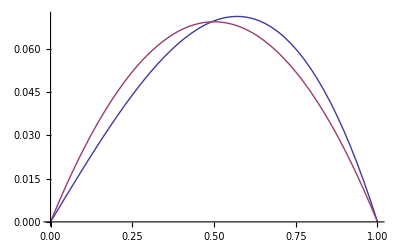

```mathematica
Plot[{Tooltip[csc(1) sin(x)-x,"exact"],Tooltip[Subscript[f, α](x)/.sol,"variational"]},{x,0,1}]
```

## Rayleigh-Ritz variational method

Consider the one-dimensional (Schrödinger) equation

-1/2ψ''(x) +V(x)ψ(x)==ℰ ψ(x),

where ψ(x) is the wavefunction (or eigenstate or eigenfunction), V(x) is the potential, and ℰ is the energy (or eigenvalue).

#### Example: one-dimensional quantum harmonic oscillator

The equation for the one-dimensional quantum harmonic oscillator with V(x)=1/2 x^2 reads

-1/2ψ''(x) +1/2 x^2 ψ(x)==ℰ ψ(x),

where -∞<x<∞ and the normalisation condition is

∫_(-∞)^∞ (ψ(x))^2 ⅆx==1.

The boundary condition is that ψ(x)→0 as x→±∞.

In this case, exact solution is possible. Here are the first four eigenstates with their corresponding energy eigenvalue:

n | ψ_n(x) | ℰ_n==n+1/2
0 | π^(-1/4)ⅇ^(-x^2/2) | 1/2
1 | √2 π^(-1/4) ⅇ^(-x^2/2) x | 3/2
2 | 1/(√2)π^(-1/4)ⅇ^(-x^2/2) (2 x^2-1) | 5/2
3 | √3 π^(-1/4)ⅇ^(-x^2/2) (2 x^3-3 x) | 7/2

The general normalized solution depends upon the n^th Hermite polynomial (HermiteH) H_n(x):

```mathematica
Subscript[ψ, n_](x_):=1/(√(2^n √π n!))Subscript[H, n](x)ⅇ^(-x^2/2)
```

The energy (in units of ℏ ω):

```mathematica
Subscript[ℰ, n_]=n+1/2;
```

Plot of the (squared) eigenstates (ψ_n(x))^2—the probability density—displaced vertically by their corresponding energy ℰ_n, superimposed onto a plot of the potential:

```mathematica
Manipulate[Plot[Evaluate[Append[Table[Tooltip[(Subscript[ψ, n](x))^p+Subscript[ℰ, n],n],{n,0,k}],x^2/2]],{x,-5,5},PlotRange->{0,7.5},AxesLabel->{x,ℰ},Filling->Table[n+1->Subscript[ℰ, n],{n,0,k}]],{{k,4},Range[0,6],SetterBar},{{p,2},Range[2]},SaveDefinitions->True]
```

#### Variational formulation

In general, it is not possible to solve the Schrödinger equation in closed-form for an arbitrary potential so usually one seeks approximate solutions.

Multiplying both sides of the Schrödinger equation by ψ(x) and integrating one obtains

∫_(-∞)^∞ ψ(x) (-1/2ψ''(x) +V(x) ψ(x)-ℰ ψ(x))ⅆx==0.

Using integration by parts and applying the boundary condition  ψ(x)→0 as x→±∞, this can be re-arranged to

ℰ==(∫_(-∞)^∞ (1/2(ψ'(x))^2+V(x) (ψ(x))^2)ⅆx)/(∫_(-∞)^∞ (ψ(x))^2 ⅆx).

The Rayleigh-Ritz variational method—a very powerful method for obtaining such approximate solutions—considers the energy as a functional, that is

ℰ[ϕ]==(∫_(-∞)^∞ (1/2(ϕ'(x))^2+V(x) (ϕ(x))^2)ⅆx)/(∫_(-∞)^∞ (ϕ(x))^2 ⅆx),

where ϕ is an approximate solution. The stationary value of ℰ[ϕ] gives an upper bound for the (lowest) eigenvalue.

#### Example: linear potential

Consider the potential

V(x)=Piecewise[{{x, 0≤x≤1}, {∞, x<0∨x>1}}]

which is linear over 0≤x≤1 and infinite outside this region. Exact solution for the energy and eigenfunctions is quite complicated and involves Airy functions. By contrast, the Rayleigh-Ritz variational method requires us to obtain stationary values of

```mathematica
ℰ[ϕ_]:=(∫_0^1 (1/2(ϕ'(x))^2+x (ϕ(x))^2)ⅆx)/(∫_0^1 (ϕ(x))^2 ⅆx)
```

In the region where the potential is infinite, ψ(x)=0, so we only need to compute the integral over 0≤x≤1.

The boundary condition is ψ(0)==ψ(1)==0. Here is a suitable one-parameter trial function (ie, our guess):

```mathematica
Subscript[ϕ, α_](x_)=α sin(π x);
```

Computing the required integrals is straightforward:

```mathematica
ℰ[Subscript[ϕ, α]]
```

1/2 (1+π^2)

Compute the numerical value:

```mathematica
N[%]
```

5.4348

This result is stationary, and is a very good approximation (an upper bound) to the exact value ℰ=5.43261…

Note that, in this case, even though the trial function contains a variational parameter α, it is not determined by the Rayleigh-Ritz variational method. This is because it is implicitly constrained by the normalisation requirement ∫_0^1 (ϕ(x))^2 ⅆx==1.